#### Problem 1

```mathematica
Q[x_,y_,z_,t_]:={3x y t,6y t, x y z t}
```

```mathematica
A[x_,y_,z_,t_]:=D[Q[x,y,z,t],t]+Q[x,y,z,t][[1]]D[Q[x,y,z,t],x]+Q[x,y,z,t][[2]]D[Q[x,y,z,t],y]+Q[x,y,z,t][[3]]D[Q[x,y,z,t],z]
```

The acceleration is

```mathematica
A[x,y,z,t]
```

{3 x y+18 t^2 x y+9 t^2 x y^2,6 y+36 t^2 y,x y z+6 t^2 x y z+3 t^2 x y^2 z+t^2 x^2 y^2 z}

#### Problem 2

```mathematica
F[x_,y_]:=x^2+y^3-y
```

```mathematica
S=Solve[Grad[F[x,y],{x,y}]=={0,0},{x,y}]
```

{{x→0,y→-1/(√3)},{x→0,y→1/(√3)}}

```mathematica
Pts = MapThread[Append,{S[[All,All,2]],F@@@S[[All,All,2]]}]
```

{{0,-1/(√3),2/(3 √3)},{0,1/(√3),-2/(3 √3)}}

```mathematica
H[x_,y_]:=D[F[x,y],{{x,y},2}]
```

```mathematica
Map[MatrixForm,H[x,y]/.S,1]
```

{(2 | 0
0 | -2 √3),(2 | 0
0 | 2 √3)}

Hessian Matrix at the first stationary point is neither positively nor negatively definite, hence it is a point of inflection. 
Hessian Matrix at the second stationary point is positively definite, hence it is a point of  minimum.

```mathematica
Show[
Plot3D[F[x,y],{x,-1,1},{y,-1,1},PlotStyle->Opacity[0.5]],
Graphics3D[{PointSize[0.024],Point/@Pts}]]
```

-Graphics3D-

#### Problem 3

(a)

```mathematica
F3[x_,y_]:=x y^2;
```

```mathematica
Grad[F3[x,y],{x,y}]
```

{y^2,2 x y}

-> ,  for some 
hence

```mathematica
(*Result: y(x)=√(2 x^2-1)*)DSolve[{y'[x]==2x/y[x],y[1]==1},y[x],x][[All,All,2]][[1,1]]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

√(-1+2 x^2)

```mathematica
(*Roll off position (1/(√2),0)*)
```

```mathematica
Solve[√(-1+2 x^2)==0,x]
```

{{x→-1/(√2)},{x→1/(√2)}}

(2)

```mathematica
T[x]:=√(-1+2 x^2);
{x,T[x],F3[x,T[x]]}
```

{x,√(-1+2 x^2),x (-1+2 x^2)}

```mathematica
Show[
Plot3D[F3[x,y],{x,0,1},{y,0,1}],
ParametricPlot3D[{x,√(-1+2 x^2),x (-1+2 x^2)},{x,0.5,1}]
]
```

-Graphics3D-

(3)

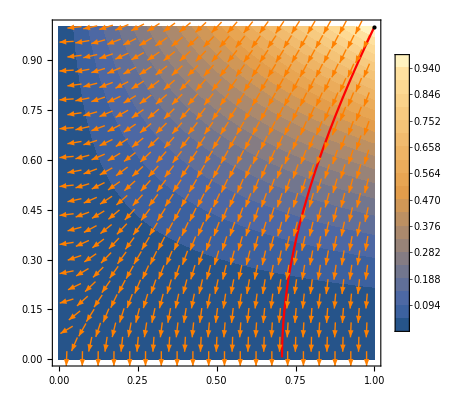

```mathematica
Vec=D[F3[x,y],#]&/@{x,y};
Show[
ContourPlot[T[x,y],{x,0,1},{y,0,1},ContourStyle->None,Contours->20,PlotLegends->Automatic,Epilog->Point[{1,1}]],
VectorPlot[-Vec,{x,0,1},{y,0,1},VectorPoints->20,VectorColorFunction->None,VectorStyle->Orange],
Plot[√(-1+2 x^2),{x,0,1},PlotStyle->Red]
]
```

#### Problem 4

(a) The second order Taylor series expansion of f(x,y) is

```mathematica
F4[x_,y_]:=Exp[-0.1x y]Sin[x y]
```

```mathematica
ep=Series[F4[x,y],{x,Pi/2,2},{y,Pi/2,2}]//Expand//Normal
```

0.487766-1.03542 (-π/2+y)-0.445131 (-π/2+y)^2+(-π/2+x) (-1.03542-1.54943 (-π/2+y)+0.863261 (-π/2+y)^2)+(-π/2+x)^2 (-0.445131+0.863261 (-π/2+y)+1.97038 (-π/2+y)^2)

```mathematica
res=0.4877662882892567-1.0354243954866662 (-π/2+y)-0.4451310298719087 (-π/2+y)^2+(-π/2+x) (-1.0354243954866662-1.5494337027023792 (-π/2+y))+(-π/2+x)^2 (-0.44513102987190867)
```

0.487766-0.445131 (-π/2+x)^2-1.03542 (-π/2+y)-0.445131 (-π/2+y)^2+(-π/2+x) (-1.03542-1.54943 (-π/2+y))

(b)

```mathematica
F4[1.4,1.7]
```

0.543919

```mathematica
(* Approximation at the point *) (res//Expand)/.{x->Pi/2,y->Pi/2}
```

0.487766

```mathematica
Show[
Plot3D[{F4[x,y],res},{x,1,2},{y,1,2},PlotLegends->{"f(x,y)","approx"},PlotStyle->Opacity[0.8]],
Graphics3D[{PointSize[0.024],Green,Point[{Pi/2,Pi/2}~Join~{F4[Pi/2,Pi/2]}]}]]
```

-Graphics3D-